# Properties of CO2 from H,P

This notebook calculates and export a .dat file, in agreement with openModelica CombiTable2D format. This allows to read the data in OpenModelica. 
The calculation is based on an exponential distribution of the points (the most needed cartography being close to the critical point).
This is done through a suite ((P_n,H_n))_n such as:
P_(n+1)=P_n+ α*(exp(β*|P_n-P_C|)-0.99)
H_(n+1)=H_n+ α'*(exp(β'*|H_n-H_C|)-0.99)
Absolute value allows to compute above and under the critical point. The -0.99 allows not to jump of minimum 1 at every step, and not to remain blocked at the critical point.
Verification is performed in order to mesure the relative error, in %. This is done through measuring this error in 10 000 random points in the region in which the points are generated.
It has to be noted that errors are big for the C_P in the region of the critical point, and subcritical region: this is because the calculation of C_P is probably done with the formula in the transient region, where it diverges. This can be seen on the following graph. Indeed, this shows that CoolProp doesn’t calculate the C_P with the quality, but with C_P = 1/T*(∂H)/(∂T). This is why, in Modelica, it is prefered to work with pressure and enthalpy: this shouldn’t be an issue, the data is just put there in case someone would need it: enthalpy can be calculated from P,S  with almost no error, and we can therefore calculate the C_P. 
The interpolationOrder chosen ensures us that it is the same interpolation as OpenModelica.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sk260350/workspace/ModelicaTable

```mathematica
PropsSI= LibraryFunctionLoad["/home/sk260350/workspace/CoolProp2/CoolProp/build/libCoolProp.so","PropsSI",{UTF8String,UTF8String,Real,UTF8String,Real,UTF8String},Real];
```

```mathematica
(PropsSI["ISENTROPIC_EXPANSION_COEFFICIENT","T",55+273.15,"P",80*10^5,"CO2"])
```

1.36456

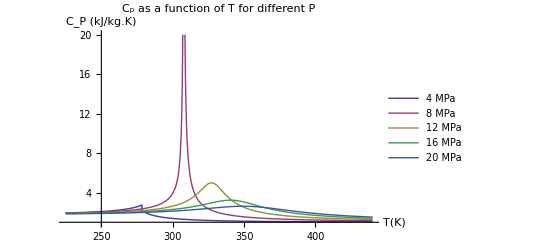

```mathematica
Plot[Evaluate[Table[PropsSI["C","T",x,"P",k*10^6,"CO2"]/1000,{k,{4,8,12,16,20}}]],{x,225,440},PlotRange->{1,20},PlotLegends->{"4 MPa","8 MPa","12 MPa","16 MPa","20 MPa"},AxesLabel->{"T(K)","C_P (kJ/kg.K)"},PlotLabel->"C_p as a function of T for different P"]
```

```mathematica
(*Discrétisation à organiser: 
-en dessous de l'état supercritique? Mieux.
- descente du nombre de points de manière logarithmique
- vérification de l'interpolation ( !: utiliser la même que Modelica), vérification avec les différentes data. Lignes de T
-écriture des fichiers txt ";*)
```

```mathematica
press=Map[N[#]&,RecurrenceTable[{P[count+1]== P[count]+0.2*10^6*(Exp[Abs[2.5*(P[count]-73.8*10^5)]/((300-60)*10^5)] -0.99), P[0] == 60*10^5},P,{count,1,350}]/10^5];
```

```mathematica
enthalp=Map[N[#]&,RecurrenceTable[{H[count+1]== H[count]+0.4*10^2*(Exp[Abs[2.5*(H[count]-499)]/((2400-250))] -0.99), H[0] == 200},H,{count,1,168}]];
```

```mathematica
temp=Map[N[#]&,RecurrenceTable[{T[count+1]== T[count]+0.2*50*(Exp[Abs[3.5*(T[count]-30.98)]/(715-20)] -0.99), T[0] == 20},T,{count,1,132}]];
```

```mathematica
"press=Table[If[k≤ 100,60+k*0.2,If[k≤ 140, 80+(k-100)*0.5,100+(k-140)]],{k,0,240}];
temp=Table[If[k≤ 50,20+k,70+(k-50)*2],{k,0,365}]";
```

```mathematica
choseFunc="T";
toInterpole=ParallelTable[{press[[tab]],enthalp[[par]],PropsSI[choseFunc,"P",press[[tab]]*100000,"H",enthalp[[par]]*1000,"CO2"]},{tab,1,Length@press},{par,1,Length@enthalp}];
funcInterpoled=Interpolation[Flatten[toInterpole,1],InterpolationOrder->1];
EcartRel[pTry_,hTry_]:=Abs[(funcInterpoled[pTry,hTry]-PropsSI[choseFunc,"P",pTry*100000,"H",hTry*1000,"CO2"])]/(PropsSI[choseFunc,"P",pTry*100000,"H",hTry*1000,"CO2"])*100
```

```mathematica
funcInterpoled[86.4,436]-273.15
```

54.6902

```mathematica
Pmin=press[[1]]
Pmax=press[[-1]]-2
Hmin=enthalp[[1]]
Hmax=enthalp[[-1]]
```

60.3292

310.695

217.031

1620.93

```mathematica
state={"T","C","D","L","S","HELMHOLTZMASS","V","CVMASS","U"};
```

```mathematica
strState={"Temperature","CP", "Density", "Conductivity","Entropy","HelmhotzEnergy","DynamicViscosity", "CV", "U"};
```

```mathematica
errors={};
plotProp={};
bigExportLoop={{"#1"}};
For[stat=1,stat≤ 9,stat++,
toInterpoleLoop=ParallelTable[{press[[tab]],enthalp[[par]],PropsSI[state[[stat]],"P",press[[tab]]*100000,"H",enthalp[[par]]*1000,"CO2"]},{tab,1,Length@press},{par,1,Length@enthalp}];
funcInterpoledLoop=Interpolation[Flatten[toInterpoleLoop,1],InterpolationOrder->1];
EcartRelLoop[pTry_,hTry_]:=Abs[(funcInterpoledLoop[pTry,hTry]-PropsSI[state[[stat]],"P",pTry*100000,"H",hTry*1000,"CO2"])]/(PropsSI[state[[stat]],"P",pTry*100000,"H",hTry*1000,"CO2"])*100;
value={};
(*If[state[[stat]]=="V",toInterpoleLoop[[All,All,3]]=toInterpoleLoop[[All,All,3]]*10^6;];
tryExpLoop=Prepend[Table[Prepend[Table[toInterpoleLoop[[k,line,3]],{k,1,Length@press}],toInterpoleLoop[[1,line,2]]*1000],{line,1,Length@enthalp}],Prepend[toInterpoleLoop[[All,1,1]]*10^5,0]];
toExportLoop=Append[Prepend[Map[Chop[N[Round[#*10^4]*10^-4]]&,tryExpLoop],{double ,strState[[stat]]<>"(" ,Length@enthalp+1,",",Length@press+1,")"}], { }];
AppendTo[bigExportLoop,toExportLoop];*)
AppendTo[plotProp,Plot3D[EcartRelLoop[x,y],{x,80,Pmax},{y,447,Hmax},ImageSize->Large,AxesLabel->{"Pressure (bar)","H (kJ/kg)","Relative error in % of "<>strState[[stat]]} ,PlotRange->All]];
value=Reap[For[k=1,k≤ 10000,k++,
pTest=RandomReal[{80,Pmax}];
hTest=RandomReal[{447,Hmax}];
Sow[{pTest,hTest,EcartRelLoop[pTest,hTest]}];]][[2,1]];
posMax=Ordering[value,1,#1[[3]]≥ #2[[3]] &];
AppendTo[errors,value[[posMax[[1]]]]];]//AbsoluteTiming
```

{961.600797,Null}

```mathematica
Export["/home/sk260350/workspace/ModelicaTable/tentativePH.dat",Flatten[bigExportLoop,1],"Data","FieldSeparators"-> " "]
```

{980.27345,Null}

/home/sk260350/workspace/ModelicaTable/tentativePH.dat

```mathematica
Grid[{Prepend[strState," "],Flatten@{"Pressure (bar)",Table[errors[[k,1]],{k,1,Length@state}]},Flatten@{"Temperature (°C)",Table[errors[[k,2]],{k,1,Length@state}]},Flatten@{"Max Relative Error (%)",Table[errors[[k,3]],{k,1,Length@state}]}},Frame->All]
```

| Temperature | CP | Density | Conductivity | Entropy | HelmhotzEnergy | DynamicViscosity | CV | U
Pressure (bar) | 304.533 | 84.9524 | 82.6702 | 85.5514 | 279.673 | 195.07 | 81.1593 | 81.0526 | 295.749
Temperature (°C) | 465.771 | 447.342 | 1575.22 | 1579.45 | 1577.53 | 588.803 | 1576.06 | 1572. | 1572.91
Max Relative Error (%) | 0.00806654 | 0.0370976 | 0.09118 | 0.135789 | 0.0163012 | -6.08027×10^-7 | 0.0185379 | 0.017683 | 0.00186227